```mathematica
<<VilCretas`
```

VilCretas está disponible.

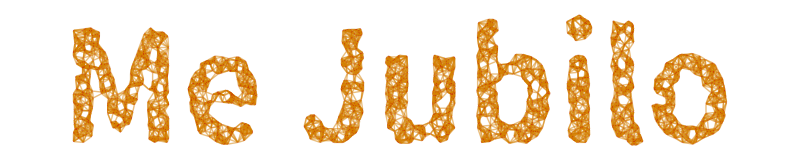

```mathematica
GrafoString["Me Jubilo"]
```

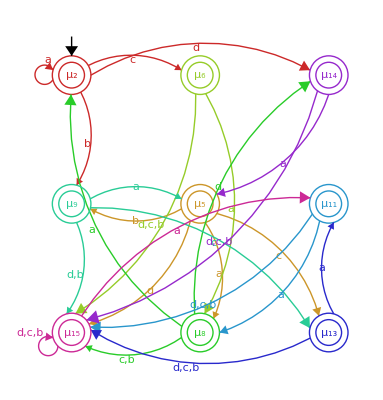

Estados: {μ_2,μ_5,μ_6,μ_8,μ_9,μ_11,μ_13,μ_14,μ_15}

Símbolos de entrada: {a,b,c,d}

Estado inicial: μ_2

Estados aceptados: {μ_2,μ_5,μ_6,μ_8,μ_9,μ_11,μ_13,μ_14,μ_15}

(  | a | b | c | d
μ_2 | μ_2 | μ_9 | μ_6 | μ_14
μ_5 | μ_8 | μ_9 | μ_13 | μ_15
μ_6 | μ_8 | μ_15 | μ_15 | μ_15
μ_8 | μ_2 | μ_15 | μ_15 | μ_14
μ_9 | μ_5 | μ_15 | μ_13 | μ_15
μ_11 | μ_8 | μ_15 | μ_15 | μ_15
μ_13 | μ_11 | μ_15 | μ_15 | μ_15
μ_14 | μ_5 | μ_15 | μ_15 | μ_15
μ_15 | μ_11 | μ_15 | μ_15 | μ_15)

Función de transición de estados con otro formato: {{μ_2,a,μ_2},{μ_2,b,μ_9},{μ_2,c,μ_6},{μ_2,d,μ_14},{μ_5,a,μ_8},{μ_5,b,μ_9},{μ_5,c,μ_13},{μ_5,d,μ_15},{μ_6,a,μ_8},{μ_6,b,μ_15},{μ_6,c,μ_15},{μ_6,d,μ_15},{μ_8,a,μ_2},{μ_8,b,μ_15},{μ_8,c,μ_15},{μ_8,d,μ_14},{μ_9,a,μ_5},{μ_9,b,μ_15},{μ_9,c,μ_13},{μ_9,d,μ_15},{μ_11,a,μ_8},{μ_11,b,μ_15},{μ_11,c,μ_15},{μ_11,d,μ_15},{μ_13,a,μ_11},{μ_13,b,μ_15},{μ_13,c,μ_15},{μ_13,d,μ_15},{μ_14,a,μ_5},{μ_14,b,μ_15},{μ_14,c,μ_15},{μ_14,d,μ_15},{μ_15,a,μ_11},{μ_15,b,μ_15},{μ_15,c,μ_15},{μ_15,d,μ_15}}

```mathematica
vectorComponentes={{s0,s1,s2,s3},{a,b,c,d},s1,{{s0,a,{s2}},{s0,b,{s3}},{s0,c,{s0,s2,s3}},{s0,d,{s0,s2}},{s1,a,{s1}},{s1,b,{s1,s3}},{s1,c,{s0,s2}},{s1,d,{s1,s2,s3}},{s2,a,{s1}},{s2,b,{s0,s1,s2,s3}},{s2,c,{s1,s2,s3}},{s2,d,{s1,s3}},{s3,a,{s0}},{s3,b,{s0,s2,s3}},{s3,c,{s3}},{s3,d,{s0,s2,s3}}},{s1,s2,s3}};

AutomataDeterministicoEquivalente[Automata[vectorComponentes[[1]],vectorComponentes[[2]],vectorComponentes[[3]],vectorComponentes[[4]],vectorComponentes[[5]]],onlyreduce->True,colores->True]

ComponentesAutomata[G]
```

```mathematica
gramatica={"A->B","A->ccb","A->bSS","A->D","A->DSC","B->SA","B->ccASC","B->c","B->SABS","C->bB","C->D","C->a","C->bbD","C->aSa","D->cSaba","D->aBABB","D->BSDaS","D->CB","D->A","S->BDSc","S->D","S->CAb","S->a","S->Dca"};

NotationBNF[gramatica]
```

<A>::=<B>

<A>::=ccb

<A>::=b<S><S>

<A>::=<D>

<A>::=<D><S><C>

<B>::=<S><A>

<B>::=cc<A><S><C>

<B>::=c

<B>::=<S><A><B><S>

<C>::=b<B>

<C>::=<D>

<C>::=a

<C>::=bb<D>

<C>::=a<S>a

<D>::=c<S>aba

<D>::=a<B><A><B><B>

<D>::=<B><S><D>a<S>

<D>::=<C><B>

<D>::=<A>

<S>::=<B><D><S>c

<S>::=<D>

<S>::=<C><A>b

<S>::=a

<S>::=<D>ca

σ^*=S

```mathematica
vectorComponentes={{A,B,C,S},{a,b,c},A,{{A,a,B},{A,b,C},{A,c,S},{B,a,B},{B,b,A},{B,c,A},{C,a,C},{C,b,A},{C,c,B},{S,a,A},{S,b,S},{S,c,C}},{B}};

AutomataToRegular[Automata[vectorComponentes[[1]],vectorComponentes[[2]],S,vectorComponentes[[4]],vectorComponentes[[5]]]]
```

Símbolos no terminales: {A,B,C,S}

Símbolos terminales: {a,b,c}

Producciones o reglas de composición: {A→a,A→aB,A→bC,A→cS,B→a,B→aB,B→bA,B→cA,C→aC,C→bA,C→c,C→cB,S→aA,S→bS,S→cC}

σ^*=S